```mathematica
(* ::Section::*)(*0. Truncated Fourier System for b_r*)
(* ===TRUNCATED FOURIER SYSTEM FOR b_r iterative solution=======================*)
ClearAll[SolveTruncatedSystemIterative, SolveTruncatedSystemDirect, ChiPlus,Theta,nL,nR,nZeta,qPlus,qMinus,HydCharge,HydCurrent];


SolveTruncatedSystemIterative[M_Integer?Positive,J_?NumericQ,gamma_?NumericQ,numIterations_:200,α_:0.4]:=
Module[{rVals,b,bNew,fMat,nGrid,rGrid,same,parity,denom,baseTerm,sums},rVals=Range[M];

(*initial b_r=1/(2π^2 r) (1-(-1)^r)*)
b=(1/(2 Pi^2 rVals)) (1-(-1)^rVals);

(*grids for n,r*)
nGrid=ConstantArray[rVals,M];
rGrid=Transpose[nGrid];
same=nGrid===rGrid;
parity=1+(-1)^(nGrid+rGrid);
denom=nGrid^4-2 nGrid^2 (rGrid^2+1)+(rGrid^2-1)^2;

fMat=Table[0.,{M},{M}];

(*n==r branch*)
Do[fMat [[i,i]]=(32.0 J^2 rVals [[i]]^2)/(1-4 rVals [[i]]^2),{i,M}];

(*n!=r branch;only even parity contributes*)
Do[
If[parity [[ i,j]]!=0,
fMat [[i,j]]=(16.0 J^2 nGrid [[i,j]] rGrid [[i,j]] parity [[i,j]])/denom [[i,j]]],{i,M},{j,M}];
baseTerm[r_]:=(1/(2 Pi^2 r)) (1-(-1)^r);

Do[sums=b.fMat;(*sums_r=Σ_n b_n f_{n,r}*)
bNew=Table[baseTerm[r]+(1/(gamma r Pi J)) sums [[r]],{r,M}];
b=α bNew+(1-α) b;(*under-relaxation*)
If[!VectorQ[b,NumericQ]||AnyTrue[b,Not@*FiniteQ],
Return[$Failed]
],
{numIterations}
];
{rVals,b}
]
(* ===TRUNCATED FOURIER SYSTEM FOR b_r, direct solution =======================*)
(*b_r=1/(2 π^2 r) (1-(-1)^r)*)
baseTerm[r_]:=(1/(2 Pi^2 r)) (1-(-1)^r);

SolveTruncatedSystemDirect[M_Integer?Positive,J_?NumericQ,gamma_?NumericQ]:=
Module[{rVals,nGrid,rGrid,parity,denom,fMat,A,rhs},

rVals= Range[M];
(*grids for n,r*)
nGrid=ConstantArray[rVals,M];
rGrid=Transpose[nGrid];
parity=1+(-1)^(nGrid+rGrid);
denom=nGrid^4-2 nGrid^2 (rGrid^2+1)+(rGrid^2-1)^2;

fMat=Table[0.,{M},{M}];

(*n==r branch*)
Do[fMat [[i,i]]=(32.0 J^2 rVals [[i]]^2)/(1-4 rVals [[i]]^2),{i,M}];
Do[
If[i!=j&&parity [[i,j]]!=0,
fMat [[i,j]]=(16.0 J^2 nGrid [[i,j]] rGrid [[i,j]] parity [[i,j]])/denom [[i,j]]],
{i,M},{j,M}
];
(*A_{r,n}=γ r π J δ_{rn}-f_{n,r}*)
A=Table[If[r==n,gamma rVals [[r]] Pi J,0.]-fMat [[n,r]],{r,M},{n,M}];
       rhs=Table[(gamma rVals [[r]] Pi J) baseTerm[rVals [[r]]],{r,M}];

{rVals,LinearSolve[A,rhs]}
];

(*---step functions and fillings---*)

Theta[x_]:=Which[x>0,1.,x<0,0.,True,0.5];

nL[k_]:=0.;
nR[k_]:=1./(4 Pi);

(*χ⁺(k)= \Theta(k)\chi^R(k) +\Theta(-k)\chi^L(k) *)
ChiPlus[k_,rVals_List,bVals_List]:=
Theta[k]*( bVals.Sin[rVals*k]) + Theta[-k] *( 1./(4. Pi) + bVals.Sin[rVals*k]);

(*n_ζ(k) with the piecewise definition,J=1 so ε'(k)=2 sin k*)
nZeta[k_,zeta_,rVals_List,bVals_List]:=
Module[{epsp,chi},
epsp=2. Sin[k];
chi=ChiPlus[k,rVals,bVals];
If[k>0,
(*k>0 branch*)
Theta[-zeta]*nL[k]+Theta[zeta]*Theta[epsp-zeta]*chi+Theta[zeta-epsp]*nR[k],
(*k<0 branch*)
Theta[zeta]*nR[k]+Theta[-zeta]*Theta[-epsp+zeta]*chi+Theta[epsp-zeta]*nL[k]
]
];

(*local single–mode charges*)
qPlus[k_,r_Integer]:=2.*Cos[r*k];
qMinus[k_,r_Integer]:=-2.*Sin[r*k];
```

```mathematica
(* ::Section::*)(* 1. Local HydCharge,HydCurrent*)


ClearAll[HydCharge,HydCurrent];

HydCharge[r_Integer,zeta_?NumericQ,sign_:"-",rVals_List,bVals_List]:=
Module[{f},
f[k_?NumericQ]:=
If[sign==="-",qMinus[k,r],qPlus[k,r]]*
nZeta[k,zeta,rVals,bVals];

NIntegrate[
f[k],
{k,-Pi,Pi},
Method->{"GlobalAdaptive","SymbolicProcessing"->0},
MinRecursion->4,
MaxRecursion->40,
AccuracyGoal->8]
];

HydCurrent[r_Integer,zeta_?NumericQ,sign_:"-",rVals_List,bVals_List]:=
Module[{f},
f[k_?NumericQ]:=
2.0*Sin[k]*If[sign==="-",qMinus[k,r],qPlus[k,r]]*
nZeta[k,zeta,rVals,bVals];

NIntegrate[f[k],
{k,-Pi,Pi},
Method->{"GlobalAdaptive","SymbolicProcessing"->0},
MinRecursion->4,
MaxRecursion->40,
AccuracyGoal->8]
];
```

```mathematica
(* ::Section::*)(*2. GHD profiles vs zeta and export*)
ClearAll[ComputeGHDProfiles];

ComputeGHDProfiles[M_Integer?Positive,
(*truncation in r*)
J_?NumericQ,gamma_?NumericQ,r_Integer,
(*charge index r*)
sign_:"-",
(*"+" or "-"*)
zetaMin_:-1.0,zetaMax_:1.0,numZeta_:201,
(* " modify this part!"*)
outDir_:"/Users/juan/Desktop/Bologna/INH_QUENCH/",tag_:""]:=
Module[{rVals,bVals,zetas,qVals,JVals,data,labelSign,plot,fileBase},
Print["Solving truncated system for b_r..."];

(* Solve truncated series for b_n, \phi_R(k)= \sum_{n=1}^\infty b_n \sin(nk) *)

(* Iterative Solution*)
(*{rVals,bVals}=SolveTruncatedSystemIterative[M,J,gamma,  400];*)

(* Linear System Solution*)
{rVals,bVals}=SolveTruncatedSystemDirect[M,J,gamma];


Print["Building zeta grid..."];

zetas=Subdivide[zetaMin,zetaMax,numZeta-1];

Print["Computing hydrodynamic charges..."];

qVals=Table[HydCharge[r,ζ,sign,rVals,bVals],{ζ,zetas}];

Print["Computing hydrodynamic currents..."];

JVals=Table[HydCurrent[r,ζ,sign,rVals,bVals],{ζ,zetas}];

(*Pack data as {zeta,q(zeta),J(zeta)}*)
data=Transpose[{zetas,qVals,JVals}];

(*Plot*)
labelSign=If[sign=="-","- sector","+ sector"];
ymin=Min[Join[qVals,JVals]];
ymax=Max[Join[qVals,JVals]];
pad=0.05 (ymax-ymin);   (*5% padding *)
plot=
Show[
{
ListLinePlot[Transpose[{zetas,qVals}],
PlotStyle->{Thick,BLue},
PlotLegends->{Style["q(ζ)",14]}
],
ListLinePlot[Transpose[{zetas,JVals}],
PlotStyle->{Thick,Red},
PlotLegends->{Style["J(ζ)",14]}
]
},
Frame->True,
FrameLabel->{Style["ζ",16],Style["q, J",16]},
PlotLabel->
Style[Row[{"GHD profiles, r = ",r,", ",labelSign,
", M = ",M,", γ = ",gamma}],16],
ImageSize->800,
GridLines->Automatic,
PlotRange-> {{zetaMin,zetaMax}, {ymin- pad, ymax+pad}}
];

(*Build a base filename*)
fileBase=FileNameJoin@{outDir,StringTemplate["GHD_r``_sign``_M``_gamma````"][r,sign,M,NumberForm[gamma,{4,2}],tag]};

(*Export data (CSV) and plot (PNG)*)
Export[fileBase<>".csv",data];

Export[fileBase<>".png",plot,"PNG",ImageResolution->300];

Print["Saved data to: ",fileBase<>".csv"];

Print["Saved plot to: ",fileBase<>".png"];

<|"Zetas"->zetas,"qVals"->qVals,"JVals"->JVals,"rVals"->rVals,"bVals"->bVals,"Plot"->plot|>]
```

Solving truncated system for b_r...

Building zeta grid...

Computing hydrodynamic charges...

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Computing hydrodynamic currents...

Saved data to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r0_sign+_M800_gamma0.10test.csv

Saved plot to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r0_sign+_M800_gamma0.10test.png

Solving truncated system for b_r...

Building zeta grid...

Computing hydrodynamic charges...

Computing hydrodynamic currents...

Saved data to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r2_sign+_M800_gamma0.10test.csv

Saved plot to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r2_sign+_M800_gamma0.10test.png

Solving truncated system for b_r...

Building zeta grid...

Computing hydrodynamic charges...

Computing hydrodynamic currents...

Saved data to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r4_sign+_M800_gamma0.10test.csv

Saved plot to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r4_sign+_M800_gamma0.10test.png

Solving truncated system for b_r...

Building zeta grid...

Computing hydrodynamic charges...

Computing hydrodynamic currents...

Saved data to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r0_sign+_M800_gamma0.50test.csv

Saved plot to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r0_sign+_M800_gamma0.50test.png

Solving truncated system for b_r...

Building zeta grid...

Computing hydrodynamic charges...

Computing hydrodynamic currents...

Saved data to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r2_sign+_M800_gamma0.50test.csv

Saved plot to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r2_sign+_M800_gamma0.50test.png

Solving truncated system for b_r...

Building zeta grid...

Computing hydrodynamic charges...

Computing hydrodynamic currents...

Saved data to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r4_sign+_M800_gamma0.50test.csv

Saved plot to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r4_sign+_M800_gamma0.50test.png

Solving truncated system for b_r...

Building zeta grid...

Computing hydrodynamic charges...

Computing hydrodynamic currents...

Saved data to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r0_sign+_M800_gamma1.00test.csv

Saved plot to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r0_sign+_M800_gamma1.00test.png

Solving truncated system for b_r...

Building zeta grid...

Computing hydrodynamic charges...

Computing hydrodynamic currents...

Saved data to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r2_sign+_M800_gamma1.00test.csv

Saved plot to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r2_sign+_M800_gamma1.00test.png

Solving truncated system for b_r...

Building zeta grid...

Computing hydrodynamic charges...

Computing hydrodynamic currents...

Saved data to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r4_sign+_M800_gamma1.00test.csv

Saved plot to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r4_sign+_M800_gamma1.00test.png

Solving truncated system for b_r...

Building zeta grid...

Computing hydrodynamic charges...

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Computing hydrodynamic currents...

Saved data to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r1_sign-_M800_gamma0.10test.csv

Saved plot to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r1_sign-_M800_gamma0.10test.png

Solving truncated system for b_r...

Building zeta grid...

Computing hydrodynamic charges...

Computing hydrodynamic currents...

Saved data to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r3_sign-_M800_gamma0.10test.csv

Saved plot to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r3_sign-_M800_gamma0.10test.png

Solving truncated system for b_r...

Building zeta grid...

Computing hydrodynamic charges...

Computing hydrodynamic currents...

Saved data to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r5_sign-_M800_gamma0.10test.csv

Saved plot to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r5_sign-_M800_gamma0.10test.png

Solving truncated system for b_r...

Building zeta grid...

Computing hydrodynamic charges...

Computing hydrodynamic currents...

Saved data to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r1_sign-_M800_gamma0.50test.csv

Saved plot to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r1_sign-_M800_gamma0.50test.png

Solving truncated system for b_r...

Building zeta grid...

Computing hydrodynamic charges...

Computing hydrodynamic currents...

Saved data to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r3_sign-_M800_gamma0.50test.csv

Saved plot to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r3_sign-_M800_gamma0.50test.png

Solving truncated system for b_r...

Building zeta grid...

Computing hydrodynamic charges...

Computing hydrodynamic currents...

Saved data to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r5_sign-_M800_gamma0.50test.csv

Saved plot to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r5_sign-_M800_gamma0.50test.png

Solving truncated system for b_r...

Building zeta grid...

Computing hydrodynamic charges...

Computing hydrodynamic currents...

Saved data to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r1_sign-_M800_gamma1.00test.csv

Saved plot to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r1_sign-_M800_gamma1.00test.png

Solving truncated system for b_r...

Building zeta grid...

Computing hydrodynamic charges...

Computing hydrodynamic currents...

Saved data to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r3_sign-_M800_gamma1.00test.csv

Saved plot to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r3_sign-_M800_gamma1.00test.png

Solving truncated system for b_r...

Building zeta grid...

Computing hydrodynamic charges...

Computing hydrodynamic currents...

Saved data to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r5_sign-_M800_gamma1.00test.csv

Saved plot to: /Users/juan/Desktop/Git/InhomogeneousQuench/C_pp/GHD_r5_sign-_M800_gamma1.00test.png

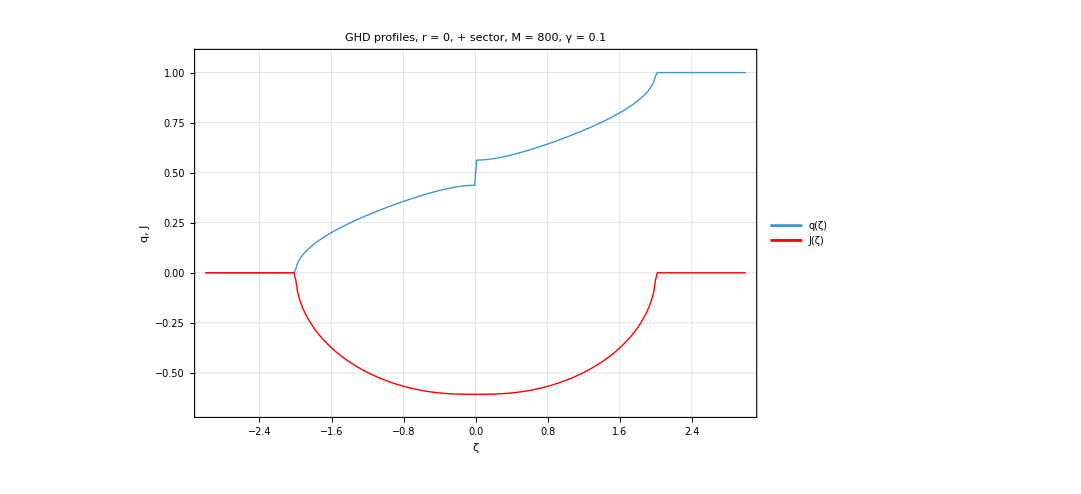

```mathematica
(* ::Section::*)(*4. Example usage*)
(*ClearAll[SolveTruncatedSystemFull,ChiPlus,Theta,nL,nR,nZeta,qPlus,qMinus,HydCharge,HydCurrent];
*)
M=800;          (*truncation in r*)
Jval=1.0;
gammas={0.1, 0.5, 1.0};
rchargeP={0,2,4}; 
rchargeM={1,3,5};

zMin=-3.0;
zMax=3.0;
nZ=300;
outDir="/Users/juan/Desktop/Git/InhomogeneousQuench/C_pp";

resultsPlus=Table[ComputeGHDProfiles[M,Jval,g,r,"+",zMin,zMax,nZ,outDir,"test"],{g,gammas},{r,rchargeP}];

resultsMinus=Table[ComputeGHDProfiles[M,Jval,g,r,"-",zMin,zMax,nZ,outDir,"test"],{g,gammas},{r,rchargeM}];

(*optional:view one plot*)
resultsPlus[[1,1,"Plot"]]
```